```mathematica
Log2[Binomial[4,2]]
```

Log[6]/Log[2]

```mathematica
Log2[2]
```

1

```mathematica
Log2[Binomial[4,2]]
```

Log[6]/Log[2]

```mathematica
N[10000-Log2[Binomial[10000,4000]]]
```

297.434

```mathematica
N[Log2[31208]]
```

14.9296

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[4000,p],k],{p,{0.5}}]//Evaluate,{k,4000},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Binomial[64,x],{x,0,64}]
```

-Graphics-

```mathematica
Sum[Binomial[1024,x],{x,0,1024}]
```

179769313486231590772930519078902473361797697894230657273430081157732675805500963132708477322407536021120113879871393357658789768814416622492847430639474124377767893424865485276302219601246094119453082952085005768838150682342462881473913110540827237163350510684586298239947245938479716304835356329624224137216

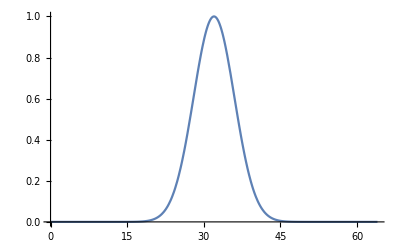

```mathematica
Plot[Exp[-(x-32)^2/(2 64/4)],{x,0,64}]
```

```mathematica
N[Integrate[1/Sqrt[2 Pi 10/4]*Exp[-(x-5)^2/(2 10/4)],{x,0,4}]]
```

0.262762

```mathematica
N[0.5*Erf[1]/(Sqrt[2*10/4])]
```

0.188434

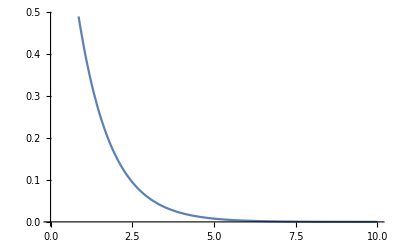

```mathematica
l := 1
M := 10
Plot[l*l*Exp[l*n]*(Exp[-2*l*n]-Exp[-2*l*(M+1)])/(1-Exp[-2*l]),{n,0,M}]
```

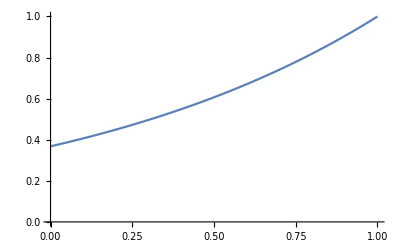

```mathematica
Plot[Exp[-l*(M-n)],{n,0,M},AxesOrigin->{0,0}]
```

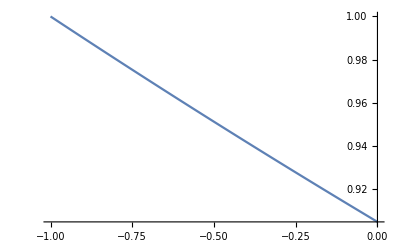

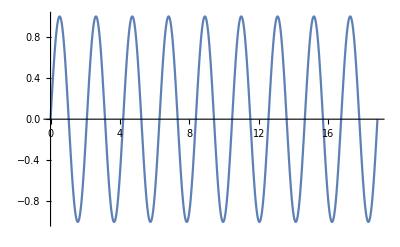

```mathematica
Plot[Exp[-l*(n+M)],{n,-M,0}]
```

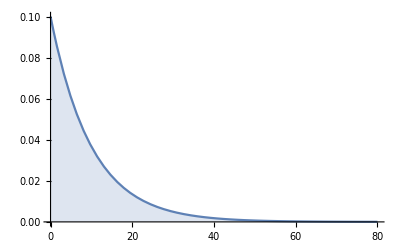

```mathematica
Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{0.100347}}]//Evaluate,{x,0,80},Filling->Axis,PlotRange->All]
```

```mathematica
l:=0.1
M:=10
Integrate[l*Exp[-l*(M-n)],{n,0,M}]
```

0.632121

```mathematica
Integrate[-l*Exp[-l*(M+n)],{n,-M,0}]
```

-0.632121

```mathematica
f[x_]:=Exp[L*(x-MM)]
f'[x]
Integrate[f'[x],{x,0,MM}]
Integrate[L*Exp[-L*x],{x,0,K}]
```

ⅇ^(L (-MM+x)) L

1-ⅇ^(-L MM)

1-ⅇ^(-K L)

```mathematica
LL:=0.001
MM:=1000
Clear[LL]
Clear[MM]
FullSimplify[LL*Integrate[Exp[-LL*x],{x,a,b}]]
```

ⅇ^(-a LL)-ⅇ^(-b LL)

```mathematica
FullSimplify[LL*Integrate[Exp[-LL*x],{x,a,Infinity}]]
```

ConditionalExpression[ⅇ^(-a LL),Re[LL]>0]

```mathematica
Integrate[LL/2*Exp[LL*x]/(Exp[LL*MM]-1),{x,a,b}]
```

(ⅇ^(a LL)-ⅇ^(b LL))/(2-2 ⅇ^(LL MM))

```mathematica
Integrate[LL/2*Exp[LL*(-x)]/(Exp[LL*MM]-1),{x,a,b}]
```

(ⅇ^(-a LL)-ⅇ^(-b LL))/(2 (-1+ⅇ^(LL MM)))

```mathematica
FullSimplify[LL/2*Integrate[Exp[LL*-n]/(Exp[LL*MM]-1),{n,-MM,0}]]
```

1/2

```mathematica
??LL
```

Parallel`Concurrency`Private`LL

```mathematica
Table[LL/2*Integrate[Exp[LL*n]/(Exp[LL*(MM+1/2)]-1)/.{LL->1,MM->1},{n,i-1/2,i+1/2}], {i, -1, 1}]
```

{((-1+ⅇ) LL)/(2 ⅇ^(3/2) (-1+ⅇ^(3/2))),((1+1/(√ⅇ)) LL)/(2 (1+√ⅇ+ⅇ)),1/2 (1-1/(1+√ⅇ+ⅇ)) LL}

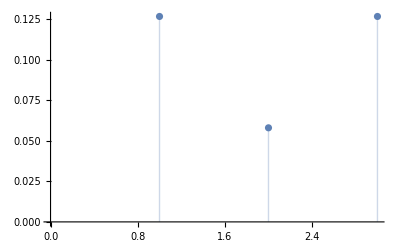

```mathematica
ListPlot[Table[LL/2*Integrate[Exp[LL*Abs[n]]/(Exp[LL*(MM+1/2)]-1)/.{LL->1,MM->2},{n,i-1/2,i+1/2}], {i, -1, 1}]/.LL->1, Filling->Axis]
```

```mathematica
0.8*Log2[1/0.4]+0.2*Log2[1/0.2]
```

1.52193

```mathematica
Log2[3.0]
```

1.58496

```mathematica
Integrate[LLL*Exp[-LLL*t],{t,0,x}]
```

1-ⅇ^(-LLL x)

1/2

```mathematica
[LL/2*Integrate[Exp[-LL*(MM-n)],{n,0,MM}]]
```

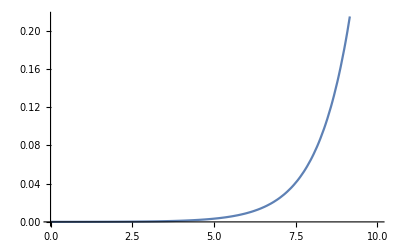

ⅇ^(L (-MM+nn))

```mathematica
Plot[Exp[x]/(2*Exp[MM]-1),{x,0,MM}]
```

```mathematica
1-1/ⅇ^3
```

1-1/ⅇ^3

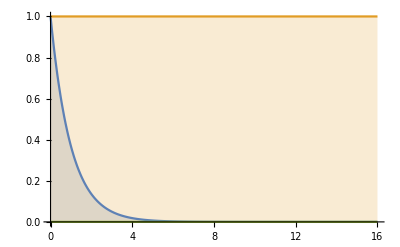

```mathematica
Plot[Table[PDF[ExponentialDistribution[λ],{x,0, 16}],{λ,{1}}]//Evaluate,{x,0,16},Filling->Axis,PlotRange->All]
```

```mathematica
1/2 E^(n t z) (-1+E^t)^-(2 n-1) ((E^t-1) (E^(t (1-z))-1))^(n-1) n t /.n->3
```

(3 ⅇ^(3 t z) (-1+ⅇ^(t (1-z)))^2 t)/(2 (-1+ⅇ^t)^3)

```mathematica
Log2[9.0]+1
```

4.16993

```mathematica
Log2[17.0]
```

4.08746

```mathematica
g[x_, n_] := n t Exp[-n t x] (Exp[t x] - 1)^(n-1)
```

```mathematica
Simplify[g[m + (z - Abs[z]) / 2, n] g[m - (z + Abs[z]) / 2, n]] /. n->1
```

ⅇ^(t (-2 m+Abs[z])) t^2

```mathematica
Integrate[%,{z,-m,m},Assumptions->{t>0,m>0}]
```

2 ⅇ^(-2 m t) (-1+ⅇ^(m t)) t

```mathematica
Out[522]/%
```

(ⅇ^(2 m t+t (-2 m+Abs[z])) t)/(2 (-1+ⅇ^(m t)))

```mathematica
FullSimplify[%,{t>0,m>0,z>0}]
```

(ⅇ^(t z) t)/(2 (-1+ⅇ^(m t)))

```mathematica
f[x_]:=Log[x Exp[x t]]
```

```mathematica
Simplify[f'[x]]
```

t+1/x

```mathematica
g[x_]:=Log[Exp[x m]-1]
```

```mathematica
Simplify[g'[x]]
```

(ⅇ^(m x) m)/(-1+ⅇ^(m x))

```mathematica
h[x_]=:Log[Exp[a x]-Exp[b x]]
```

```mathematica
h'[x]
```

(a ⅇ^(a x)-b ⅇ^(b x))/(ⅇ^(a x)-ⅇ^(b x))

```mathematica
h''[x]
```

-((a ⅇ^(a x)-b ⅇ^(b x))^2)/((ⅇ^(a x)-ⅇ^(b x))^2)+(a^2 ⅇ^(a x)-b^2 ⅇ^(b x))/(ⅇ^(a x)-ⅇ^(b x))

```mathematica
F[x_]:=a Exp[b x]
```

```mathematica
Integrate[F[x],{x,0,Infinity},Assumptions->{a>0, b<0}]
```

-a/b

```mathematica
4195226/3800316.0
```

1.10392

```mathematica
4651301/4358887.0
```

1.06708

```mathematica
2828070/2562960.0
```

1.10344

```mathematica
Integrate[lambda/2 Exp[lambda Abs[x]]/(Exp[lambda m]-1), {x,-m,m},Assumptions->{m>0}]
```

1

```mathematica
m=8
lambda=0.00295633
```

8

0.00295633

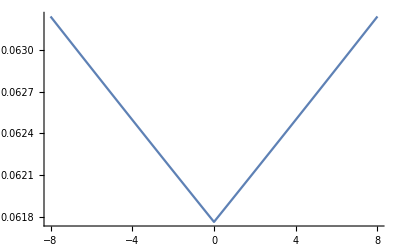

```mathematica
Plot[lambda/2 Exp[lambda Abs[x]]/(Exp[lambda m]-1), {x,-m,m},AxesOrigin->{0,0},PlotRange->All]
```

0.00154113

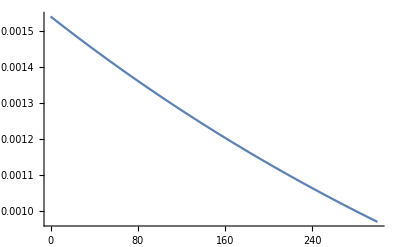

```mathematica
lambda =0.00154113
Plot[lambda Exp[-lambda x], {x,0,300},AxesOrigin->{0,0},PlotRange->All]
```